```mathematica
(* IMPORT MODULES *)
SetDirectory[NotebookDirectory[]];
NotebookEvaluate["modules/oscillator_bracket.nb"];
NotebookEvaluate["modules/operators.nb"];
NotebookEvaluate["modules/mews_and_alphas.nb"];
```

```mathematica
(* INITIALIZING PARAMETERS *)
uq=0.315 (* up quark mass *);
sq=0.577 (* strange quark mass *);
cq=1.836(* charm quark mass *);
bq=5.227 (* bottom quark mass *);
sigma=0.1653; (* coefficient of string strength term *)
alphaCoulomb=0.5069; (* coefficient of Coulomb term (0.0175) if you want to replicate Roberts *)
Cqqq=-0.8321(* V = -Subscript[α, C]/r + σr + Subscript[C, qqq] *);
κp=1.8609(* Thing in the spin term *);
CF=1/2(* Colour Factor *);
```

```mathematica
(* THIS FUNCTION RETURNS THE BARYON HAMILTONIAN FOR A GIVEN ω *)
baryonHamiltonian[J_,P_,Isospin_,Λ_,γMax_,omega_,m1_,m2_,m3_]:=baryonHamiltonian[J,P,Isospin,Λ,γMax,omega,m1,m2,m3]=(
ω=omega;
projector=Projector[J,P,Λ,γMax,Isospin];
sM=stateMatrix[J,P,Λ,γMax];
vCoulomb=polynomialOperatorRho[sM,-1];
vLinear=polynomialOperatorRho[sM,1];
spinPart12=(8 Pi)/(3m1 m2 r0[m1,m2]^3 Pi^(3/2))κp*GaussOperator[sM,ω,3,m1,m2,m3];
spinPart23=(8 Pi)/(3m2 m3 r0[m2,m3]^3 Pi^(3/2))κp*Transpose[t1].GaussOperator[sM,ω,1,m1,m2,m3].t1;
spinPart31=(8 Pi)/(3m3 m1 r0[m3,m1]^3 Pi^(3/2))κp*Transpose[t2].GaussOperator[sM,ω,2,m1,m2,m3].t2;

v12baryon=-alphaCoulomb*α[m1,m2]*vCoulomb+(sigma*vLinear)/α[m1,m2]+spinPart12;
v23baryon=-alphaCoulomb*α1[m1,m2,m3]*(Transpose[t1].vCoulomb.t1)+(sigma*(Transpose[t1].vLinear.t1))/α1[m1,m2,m3]+spinPart23;
v31baryon=-alphaCoulomb*α2[m1,m2,m3]*(Transpose[t2].vCoulomb.t2)+(sigma*(Transpose[t2].vLinear.t2))/α2[m1,m2,m3]+spinPart31;
kin=kMatrix[sM,omega,m1,m2,m3];
mas1=IdentityMatrix[size]*m1;
mas2=IdentityMatrix[size]*m2;
mas3=IdentityMatrix[size]*m3;
cqqq=IdentityMatrix[size]*(Cqqq);
kinetic=mas1+mas2+mas3+kin;
Hbaryon=kinetic+CF(v12baryon+v23baryon+v31baryon+3*cqqq);
Hbaryon=ApplyProjector[Hbaryon,projector])
```

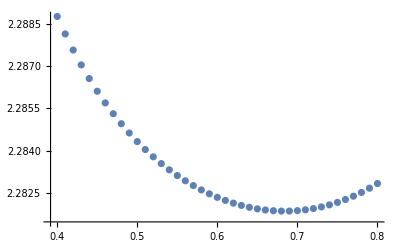

Successfully Found Minimum

{0.68,2.28186}

```mathematica
(* INITIALIZING HYPERPARAMETERS *)
J=1/2;
P=+1;
Isospin=0;
γMax=8;
Λ=0;
m1=uq;
m2=uq;
m3=cq;
t1=tMatrix[J,P,Λ,γMax,m1,m2,m3,1];
t2=tMatrix[J,P,Λ,γMax,m1,m2,m3,2];
projector=Projector[J,P,Λ,γMax,Isospin];
size=Dimensions[t1][[1]];
r0[mi_,mj_]:=1.6553((2mi mj)/(mi+mj))^-0.2204(* Gaussian function parameter *);
firstNonZero=size-Total[Diagonal[projector]]+1;
tab=Table[{ω,Eigenvalues[baryonHamiltonian[J,P,Isospin,Λ,γMax,ω,m1,m2,m3]][[-firstNonZero]]-(2.02*10^-3)/(m1*m2*m3)},{ω,0.4,0.8,0.01}];
ListPlot[tab]
omegas=tab[[All,1]];
evals=tab[[All,2]];
minEval=Min[evals];
posOfMinEval=Position[evals,minEval][[1,1]];
optimumOmega=omegas[[posOfMinEval]];
minimum={optimumOmega,minEval};
errors=0;
If[tab[[posOfMinEval]]!=minimum,errors+=1;Print["Does not agree"]]
If[posOfMinEval==1,errors+=1;Print["Need to extend range more to the left"]]
If[posOfMinEval==Length[tab],errors+=1;Print["Need to extend range more to the right"]]
If[errors==0,Print["Successfully Found Minimum"];Print[minimum]]
```